# Conformal Barycenter Sampling Examples

This notebook demonstrates the use of the conformal barycenter sampler by computing some example histograms for functions where we know the expected answers and comparing the results.

```mathematica
Exit
```

## Loading the sampler

The first step in using the barycenter sampling package is loading the sampler. From this example file, it’s one directory up:

```mathematica
Get[Echo@FileNameJoin[{ParentDirectory[NotebookDirectory[]],"CoBarSLink.m"}]]
CoBarSLink`Private`clearLibraries[]
```

/Users/jasoncantarella/CoBarSLink/CoBarSLink.m

but you should alter the path accordingly if you’re working elsewhere.

Get an overview over the most important symbols this way:

```mathematica
?CoBarSLink`*
```

## CoBarSample

The first function in the library is CoBarSample:

```mathematica
?CoBarSample
```

CoBarSample collects sample values for a list of different geometric quantities. To save time, the function to sample must be written in C++ and included in the CoBarS source tree. 
The currently coded functions are:

“BarycenterNorm” -- the (Euclidean) norm of the conformal barycenter of the open polygon generated (before conformal closure)
“BendingEnergy”[p] -- 
“ChordLength”[a,b] -- the distance between vertex a and vertex b of the closed polygon
“DiagonalLength” -- the distance between the first vertex and the middle (Floor[n/2]) vertex of the closed polygon

The edgelength vector r must have the property that no single edge has more than half the total length of the polygon.

```mathematica
result=CoBarSample["Gyradius",3,{5,1,1,1},10]
```

CoBarSLink::badedgelengths: One edge has more than half the total length of the polygon. No closed polygons with these edgelengths exist.

$Failed

Some further failure modes.

```mathematica
result=CoBarSample["Gyradius",3,{1,1,1,1},10,"SphereRadii"->anything]
```

CoBarSLink::badsphereradii2: The value for the option "SphereRadii" has to be a numerical vector or a String.

$Failed

```mathematica
result=CoBarSample["Gyradius",3,{1,1,1,1},10,"SphereRadii"->{1,1}]
```

CoBarSLink::badsphereradii: The Length of the vector given as value for option "SphereRadii" does not coincide with the Length of the second argument.

$Failed

```mathematica
result=CoBarSample["Some random text",3,{1,1,1,1},10]
```

Compiling cSampleRandomVariables[3]...

Reading build settings from /Users/jasoncantarella/CoBarSLink/LibraryResources/Source/BuildSettings.m

Compilation done. Time elapsed = 8.115 s.

ERROR: cSampleRandomVariables: Random variable with tag "Some" not found. Aborting.

$Failed

Sampling 1 million 4-gons in 3 dimensional space is very fast:

```mathematica
First@AbsoluteTiming[
result=CoBarSample["Gyradius",3,{1,1,1,1},1000000];
]
```

0.227405

0.227828

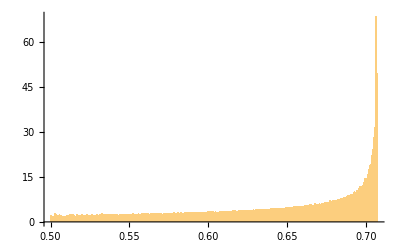

```mathematica
First@AbsoluteTiming[
result=CoBarSample["Gyradius",3,{1,1,1,1},1000000];
]

Histogram[result,"Wand","PDF"]
```

You can sample several random variables at once with little extra cost, although constructing the histogram still takes a surprisingly long time:

```mathematica
result=CoBarSample[
{"Gyradius","SquaredGyradius","TotalCurvature","ChordLength"[1,3]},3,{1,1,1,1},1000000
];
```

0.280303

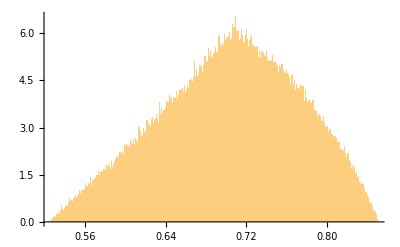
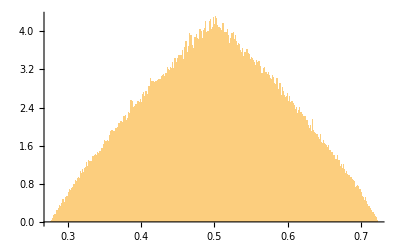
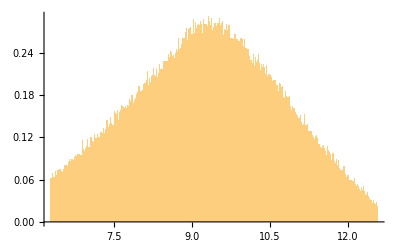
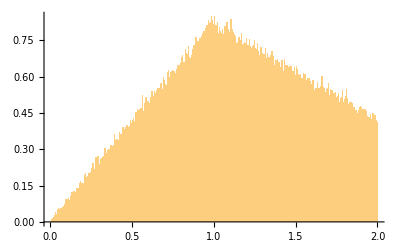
{6.67174,<|Gyradius→-Graphics-,SquaredGyradius→-Graphics-,TotalCurvature→-Graphics-,ChordLength[1,3]→-Graphics-|>}

```mathematica
First@AbsoluteTiming[
result=CoBarSample[
{"Gyradius","SquaredGyradius","TotalCurvature","ChordLength"[1,3]},3,{1,1,1,1,1},1000000
];
]

Timing[Histogram[#,1000,"PDF"]&/@result]
```

0.549821

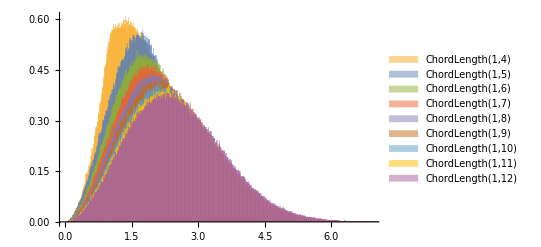

```mathematica
First@AbsoluteTiming[
result=CoBarSample[Table["ChordLength"[1,k],{k,4,12}],3,ConstantArray[1,32],1000000,"QuotientSpace"->True];
]
Histogram[result,"Wand","PDF",ChartLegends->Automatic]
```

We can sample in 3D...

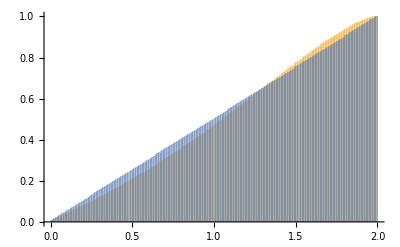

```mathematica
result1=CoBarSample["ChordLength"[1,3],3,ConstantArray[1,4],1000000,"QuotientSpace"->False];
result2=CoBarSample["ChordLength"[1,3],3,ConstantArray[1,4],1000000,"QuotientSpace"->True];

Histogram[{result1,result2},"Wand","CDF"]
```

... we can sample in 4D...

Compiling cSampleRandomVariables[4]...

Compilation done. Time elapsed = 2.74309 s.

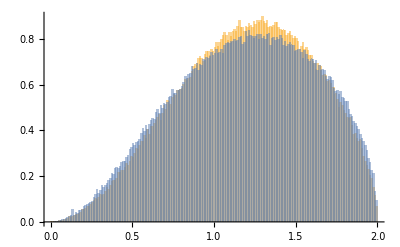

```mathematica
result1=CoBarSample["ChordLength"[1,3],4,ConstantArray[1,6],1000000,"QuotientSpace"->False];
result2=CoBarSample["ChordLength"[1,3],4,ConstantArray[1,6],1000000,"QuotientSpace"->True];

Histogram[{result1,result2},"Wand","PDF"]
```

... we can also sample in 2D...

Compiling cSampleRandomVariables[2]...

Compilation done. Time elapsed = 2.475 s.

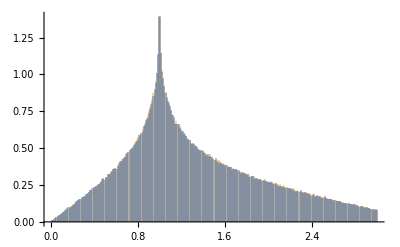

```mathematica
result1=CoBarSample["ChordLength"[1,4],2,ConstantArray[1,8],1000000,"QuotientSpace"->False];
result2=CoBarSample["ChordLength"[1,4],2,ConstantArray[1,8],1000000,"QuotientSpace"->True];

Histogram[{result1,result2},"Wand","PDF"]
```

... or in any other (not too large) dimension. The libraries will be JIT-compiled the first time they are called.

Compiling cSampleRandomVariables[6]...

Compilation done. Time elapsed = 2.81714 s.

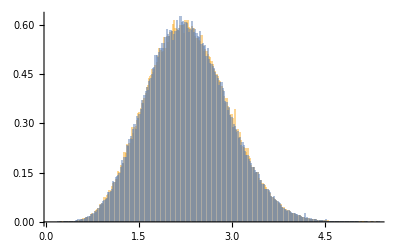

```mathematica
result1=CoBarSample["ChordLength"[1,8],6,ConstantArray[1,32],1000000,"QuotientSpace"->False];
result2=CoBarSample["ChordLength"[1,8],6,ConstantArray[1,32],1000000,"QuotientSpace"->True];

Histogram[{result1,result2},"Wand","PDF"]
```

FYI: This lists the paths of the dynamic libraries generated:

```mathematica
CoBarSLink`Private`listLibraries[]
```

{/Users/jasoncantarella/CoBarSLink/LibraryResources/MacOSX-ARM64/SampleRandomVariables_2D.dylib,/Users/jasoncantarella/CoBarSLink/LibraryResources/MacOSX-ARM64/SampleRandomVariables_3D.dylib,/Users/jasoncantarella/CoBarSLink/LibraryResources/MacOSX-ARM64/SampleRandomVariables_4D.dylib,/Users/jasoncantarella/CoBarSLink/LibraryResources/MacOSX-ARM64/SampleRandomVariables_6D.dylib}

This deletes the libraries and restarts the package:

```mathematica
CoBarSLink`Private`clearLibraries[]
```

```mathematica
CoBarSLink`Private`listLibraries[]
```

{}

## RandomPolygons

```mathematica
?RandomClosedPolygons
```

```mathematica
d=3;
n=64;
samplecount=1000000;
dataCoBarS=RandomClosedPolygons[d,ConstantArray[1.,n],samplecount,
"QuotientSpace"->True,
"SphereRadii"->ConstantArray[1.,n]
];//AbsoluteTiming

dataCoBarS//Keys
```

Compiling cRandomClosedPolygons_3D_Xoshiro_1_0...

Reading build settings from /Users/jasoncantarella/CoBarSLink/LibraryResources/Source/BuildSettings.m

Compilation done. Time elapsed = 2.29599 s.

{3.45683,Null}

{VertexPositions,SamplingWeights,EdgeLengths,SphereRadii,QuotientSpace}

The generated polygons are not only closed, they are also such that their center of mass lies in the origin.

```mathematica
centersofmass=Mean/@dataCoBarS["VertexPositions"][[All,1;;-2]];
Max[Norm/@centersofmass]
```

2.93022×10^-13

To compute the sampling mean you have to use the “SamplingWeights” in the returned data structure as follows:

```mathematica
(*We may compute like this because the center of mass vanishes.*)
squaredGyradii=Total[dataCoBarS[["VertexPositions",All,1;;-2]]^2,{2,3}]/n;
samplingAverage=squaredGyradii.dataCoBarS["SamplingWeights"]/Total[dataCoBarS["SamplingWeights"]]
```

5.41797

## ActionAngleSample

You can also use the Progressive Action Angle Method to generate closed polygons.

```mathematica
?ActionAngleSample
```

```mathematica
dataPAAM=ActionAngleSample[n,samplecount];//AbsoluteTiming

dataPAAM//Keys
```

Compiling cActionAngleSample_Progressive...

Compilation done. Time elapsed = 1.033 s.

{2.97635,Null}

{VertexPositions,Trials}

These polygons also  have center of mass at the origin:

```mathematica
centersofmass=Mean/@dataPAAM["VertexPositions"][[All,1;;-2]];
Max[Norm/@centersofmass]
```

4.53709×10^-15

```mathematica
squaredGyradii=Total[dataPAAM["VertexPositions"][[All,1;;-2]]^2,{2,3}]/n;
samplingAverage=Mean[squaredGyradii]
```

5.41396